# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineages other, Delta, Omicron BA.1, Omicron BA.2, Omicron BA.4 and Omicron BA.5.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-south-africa-ba4-ba5

```mathematica
dataset="omicron-south-africa-ba4-ba5";
```

```mathematica
imageSize=280;
```

```mathematica
gridCount=2;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron BA.1","Omicron BA.2","Omicron BA.4","Omicron BA.5"};
```

```mathematica
n=Length[variants]
```

6

### Colors

```mathematica
start[n_]:=0.1;
```

```mathematica
stop[n_]:=0.98;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Prepend[makeColors[n-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.31246632, 0.59399708, 0.72838912],RGBColor[0.5737267600000001, 0.73875072, 0.38814183999999996],RGBColor[0.86951232, 0.6566998, 0.23336048],RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001]}

```mathematica
legendPanel=PointLegend[colors[[2;;n]],variants[[2;;n]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Locations

```mathematica
locationsToDrop={"Mpumalanga","Western Cape Province"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2022-01-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-04-04

```mathematica
countries=Union[seqData[[All,2]]]
```

{Gauteng,KwaZulu-Natal,Mpumalanga,Western Cape Province}

```mathematica
countries=Complement[countries,locationsToDrop]
```

{Gauteng,KwaZulu-Natal}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-10;;-1]]&,countries]
```

{Gauteng→{{2022-03-26,1},{2022-03-27,0},{2022-03-28,0},{2022-03-29,9},{2022-03-30,7},{2022-03-31,0},{2022-04-01,0},{2022-04-02,0},{2022-04-03,0},{2022-04-04,0}},KwaZulu-Natal→{{2022-03-26,0},{2022-03-27,0},{2022-03-28,0},{2022-03-29,0},{2022-03-30,0},{2022-03-31,5},{2022-04-01,15},{2022-04-02,4},{2022-04-03,1},{2022-04-04,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=30;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_,index_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[index]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_,index_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[index]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountriesBA4=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron BA.4"],countrySequenceCounts[#]]]}&,countries]
```

{{{{2022-03-02,-2.09748},{2022-03-03,-2.00251},{2022-03-04,-1.90754},{2022-03-05,-1.81258},{2022-03-06,-1.71761},{2022-03-07,-1.62264},{2022-03-08,-1.52768},{2022-03-09,-1.43271},{2022-03-10,-1.33774},{2022-03-11,-1.24277},{2022-03-12,-1.14781},{2022-03-13,-1.05284},{2022-03-14,-0.957872},{2022-03-15,-0.862905},{2022-03-16,-0.767937},{2022-03-17,-0.67297},{2022-03-18,-0.578003},{2022-03-19,-0.483035},{2022-03-20,-0.388068},{2022-03-21,-0.293101},{2022-03-22,-0.198134},{2022-03-23,-0.103166},{2022-03-24,-0.00819901},{2022-03-25,0.0867683},{2022-03-26,0.181736},{2022-03-27,0.276703},{2022-03-28,0.37167},{2022-03-29,0.466637},{2022-03-30,0.561605},{2022-03-31,0.656572},{2022-04-01,0.751539}}},{{{2022-03-02,-2.54676},{2022-03-03,-2.56804},{2022-03-04,-2.58932},{2022-03-05,-2.6106},{2022-03-06,-2.63188},{2022-03-07,-2.65316},{2022-03-08,-2.67444},{2022-03-09,-2.69572},{2022-03-10,-2.717},{2022-03-11,-2.73828},{2022-03-12,-2.75956},{2022-03-13,-2.78084},{2022-03-14,-2.80212},{2022-03-15,-2.8234},{2022-03-16,-2.84468},{2022-03-17,-2.86596},{2022-03-18,-2.88724},{2022-03-19,-2.90851},{2022-03-20,-2.92979},{2022-03-21,-2.95107},{2022-03-22,-2.97235},{2022-03-23,-2.99363},{2022-03-24,-3.01491},{2022-03-25,-3.03619},{2022-03-26,-3.05747},{2022-03-27,-3.07875},{2022-03-28,-3.10003},{2022-03-29,-3.12131},{2022-03-30,-3.14259},{2022-03-31,-3.16387},{2022-04-01,-3.18515}}}}

```mathematica
modeledFreqsForCountriesBA5=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron BA.5"],countrySequenceCounts[#]]]}&,countries]
```

{{{{2022-03-02,-4.71884},{2022-03-03,-4.6475},{2022-03-04,-4.57616},{2022-03-05,-4.50482},{2022-03-06,-4.43348},{2022-03-07,-4.36213},{2022-03-08,-4.29079},{2022-03-09,-4.21945},{2022-03-10,-4.14811},{2022-03-11,-4.07677},{2022-03-12,-4.00542},{2022-03-13,-3.93408},{2022-03-14,-3.86274},{2022-03-15,-3.7914},{2022-03-16,-3.72005},{2022-03-17,-3.64871},{2022-03-18,-3.57737},{2022-03-19,-3.50603},{2022-03-20,-3.43469},{2022-03-21,-3.36334},{2022-03-22,-3.292},{2022-03-23,-3.22066},{2022-03-24,-3.14932},{2022-03-25,-3.07797},{2022-03-26,-3.00663},{2022-03-27,-2.93529},{2022-03-28,-2.86395},{2022-03-29,-2.79261},{2022-03-30,-2.72126},{2022-03-31,-2.64992},{2022-04-01,-2.57858}}},{{{2022-03-02,-3.26062},{2022-03-03,-3.14682},{2022-03-04,-3.03303},{2022-03-05,-2.91923},{2022-03-06,-2.80543},{2022-03-07,-2.69164},{2022-03-08,-2.57784},{2022-03-09,-2.46404},{2022-03-10,-2.35025},{2022-03-11,-2.23645},{2022-03-12,-2.12265},{2022-03-13,-2.00885},{2022-03-14,-1.89506},{2022-03-15,-1.78126},{2022-03-16,-1.66746},{2022-03-17,-1.55367},{2022-03-18,-1.43987},{2022-03-19,-1.32607},{2022-03-20,-1.21228},{2022-03-21,-1.09848},{2022-03-22,-0.984681},{2022-03-23,-0.870884},{2022-03-24,-0.757087},{2022-03-25,-0.64329},{2022-03-26,-0.529493},{2022-03-27,-0.415696},{2022-03-28,-0.301899},{2022-03-29,-0.188102},{2022-03-30,-0.0743046},{2022-03-31,0.0394925},{2022-04-01,0.153289}}}}

```mathematica
legendsForCountriesBA4=Map[constructGrowthRateLegend[modeledGrowthRate[#[[5]]],variants[[5]],legendStartingPointY- 0.09,colors[[5]]]&,freqsForCountries]
```

{{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86951232, 0.6566998, 0.23336048],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.09 per day (0.08, 0.11),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}},{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86951232, 0.6566998, 0.23336048],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = -0.02 per day (-0.18, 0.13),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}}}

```mathematica
legendsForCountriesBA5=Map[constructGrowthRateLegend[modeledGrowthRate[#[[6]]],variants[[6]],legendStartingPointY- 0.09,colors[[6]]]&,freqsForCountries]
```

{{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.07 per day (0.06, 0.08),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}},{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.11 per day (0.09, 0.14),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}}}

```mathematica
Join[legendsForCountriesBA4,legendsForCountriesBA5]
```

{{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86951232, 0.6566998, 0.23336048],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.09 per day (0.08, 0.11),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}},{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86951232, 0.6566998, 0.23336048],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = -0.02 per day (-0.18, 0.13),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}},{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.07 per day (0.06, 0.08),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}},{GrayLevel[1],Rectangle[Scaled[{0.01,0.81}],Scaled[{0.82,0.91}]],{RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001],PointSize[0.03],Point[Scaled[{0.04,0.87}]],GrayLevel[0],Text[r = 0.11 per day (0.09, 0.14),Scaled[{0.075,0.86}],{-1,0},Background→GrayLevel[1]]}}}

```mathematica
panelA=logisticFreqPlotMultipleLineages[freqsForCountries[[1]],modeledFreqsForCountriesBA4[[1]],legendsForCountriesBA4[[1]],countries[[1]],5]
```

-Graphics-

```mathematica
panelB=logisticFreqPlotMultipleLineages[freqsForCountries[[2]],modeledFreqsForCountriesBA5[[2]],legendsForCountriesBA5[[2]],countries[[2]],6]
```

-Graphics-

```mathematica
panels={panelA,panelB};
```

```mathematica
figLogistic=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_logistic-growth-transformed-axis.png

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[1,-2,-5;;-1]]
```

{{2022-03-28,0.523807},{2022-03-29,0.588232},{2022-03-30,0.624996},{2022-03-31,0.624996},{2022-04-01,0.624996}}

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[2,-1,-5;;-1]]
```

{{2022-03-28,0.099999},{2022-03-29,0.549997},{2022-03-30,0.583331},{2022-03-31,0.559998},{2022-04-01,0.559998}}

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

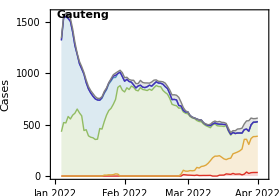
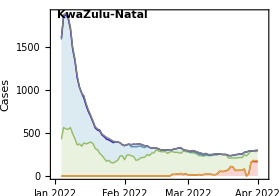
| 
-Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=250000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron 21L"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[4]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron 21L"]],"Omicron 21L",legendStartingPointY- 0.09,colors[[4]]]&,countries];
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of LinearModelFit[{},{1,x},x][BestFitParameters] does not exist.

Part::partw: Part 2 of LinearModelFit[{},{1,x},x][ParameterConfidenceIntervals] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_partitioned-log-cases.png